### lib

```mathematica
SetOptions[{Plot, ListPlot,RegionPlot},GridLines->Automatic];
```

```mathematica
ToV[x_]:=x//Normal//Values;
```

```mathematica
GIndex[mean_,σ_,ksi_]:=ksi/σ^2+(ⅇ^(-mean^2/(2 σ^2)) σ)/(√(2 π))+1/2 mean (1+Erf[mean/(√2 σ)]);
MossIndex[mean_,σ_, l_,psi_]:=(mean+σ*Sqrt[Max[psi,l+Log[σ]]]);

PIndex[mean_,σ_, l_]:=mean + l *σ;
```

```mathematica
meanB0=-0.5;sigmaB0=1.0;l0=1.1; a0=0.09; b0=0.5;ms0=0.75;
```

```mathematica
Manipulate[
RegionPlot[
{
PIndex[mean,sigma,l]< PIndex[meanB,sigmaB,l],
GIndex[mean,sigma,0.0]< GIndex[meanB,sigmaB,0.0],
MossIndex[mean,ms * sigma,(l+a)^2,(l +a- b)^2]< MossIndex[meanB,ms * sigmaB,(l+a)^2,(l +a-b)^2]
},
{mean, -1.2,0.5},
{sigma, 0.1,1.2}
],
{{meanB, -0.5}, -2,0},
{{sigmaB, 1}, 0.1,2},
{{l, l0}, 0.1,2},
{{ms, ms0}, 0.7,1.2},
{{a, a0}, -0.5,1.0},
{{b, b0}, -0.5,1.0}
]
```

### Import

```mathematica
file="~/projects/shipit_all/shipit/shipit_results.txt";
```

```mathematica
fields=StringSplit[
"result\tresult_sigma\tm\tseed\tweeks\ttrials\tmean\tsigma\terror\tp1\tp2\tp3\tp4\tp5","\t"
];
intFields={"m", "seed", "weeks", "trials"};
types = Association[(#->"Number")&/@fields];
(types[#]="Integer";)&/@intFields;
types
```

<|result→Number,result_sigma→Number,m→Integer,seed→Integer,weeks→Integer,trials→Integer,mean→Number,sigma→Number,error→Number,p1→Number,p2→Number,p3→Number,p4→Number,p5→Number|>

```mathematica
data0=SemanticImport[file, types]
```

Dataset[<>]

```mathematica
KeyFn[r_]:=HK[r["m"],r["mean"],r["sigma"],r["error"]];
dataHash=<||>;
(
r=#;
k=KeyFn[r];
If[
Lookup[dataHash, k,Null]==Null || 
dataHash[k]["weeks"]<r["result"]||
dataHash[k]["result"]<r["result"],
dataHash[k]=r
];
)&/@data0[Select[#["weeks"]≥10000&]];

data=(Dataset[Values[dataHash]]//Sort );
```

```mathematica
{Length[data0],Length[dataHash]}
```

{1292,1292}

### mean = -1, sigma = 1. Plot result vs error

```mathematica
prefilteredData=data[Select[ #["sigma"]==1 && #["mean"]==-1& ]]//Sort;
```

```mathematica
prefilteredData[Select[( #["error"]==35) && #["sigma"]==1 & ]]//Sort
```

```mathematica
d1=prefilteredData[Select[(#["m"]==1) && #["sigma"]==1  & ]]//Sort;
d5=prefilteredData[Select[( #["m"]==5) && #["sigma"]==1  & ]]//Sort;
d52=prefilteredData[Select[( #["m"]==52) && #["sigma"]==1  & ]]//Sort;
d51=prefilteredData[Select[( #["m"]==51) && #["sigma"]==1  & ]]//Sort;
d7=prefilteredData[Select[( #["m"]==7) && #["sigma"]==1  & ]]//Sort;
d71=prefilteredData[Select[( #["m"]==71) && #["sigma"]==1  & ]]//Sort;
```

```mathematica
d7
```

```mathematica
d51
```

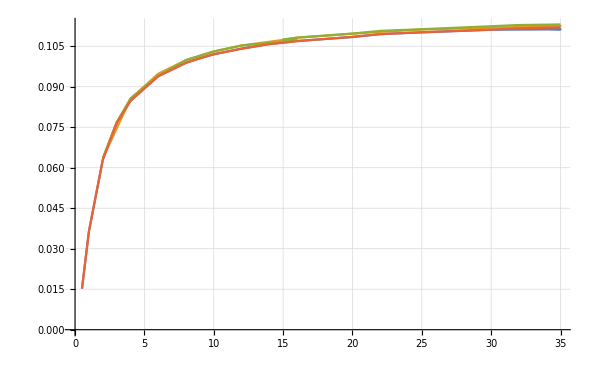

```mathematica
ListPlot[
{
d5[All, {"error", "result"}],
d52[All, {"error", "result"}],
d7[All, {"error", "result"}],
d1[All, {"error", "result"}]
},
Joined->True]
```

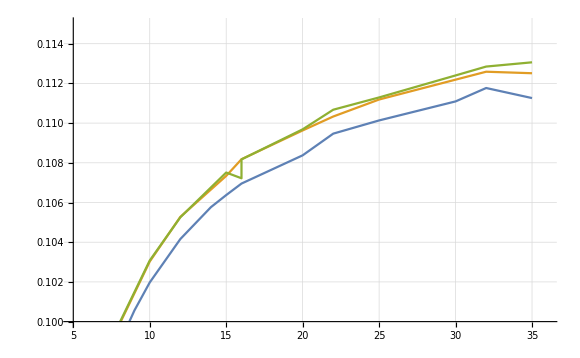

```mathematica
ListPlot[
{
d5[All, {"error", "result"}]//Sort,
d52[All, {"error", "result"}]//Sort,
d7[All, {"error", "result"}]//Sort
},
Joined->True,PlotRange->{{5,36},{0.10,0.115}}
]
```

```mathematica
ResultVsError[data_, mean_, sigma_, methods_]:=Module[
{prefilteredData, method},
prefilteredData=data[Select[ #["sigma"]==sigma && #["mean"]==mean& ]]//Sort;
(
method = #;
prefilteredData[Select[(#["m"]==method)& ], {"error", "result"}]//Sort
)&/@methods
]
```

```mathematica
dss=ResultVsError[data, -1, 1, {5,52,7}]
```

{,,}

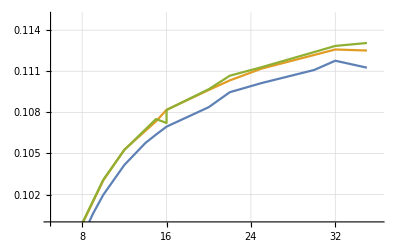

```mathematica
ListPlot[
dss,
Joined->True,PlotRange->{{5,36},{0.10,0.115}}
]
```

### mean = -0.5, sigma = 1. Plot result vs error

```mathematica
dss=ResultVsError[data, -0.5, 1, {5,52,7,71}];
```

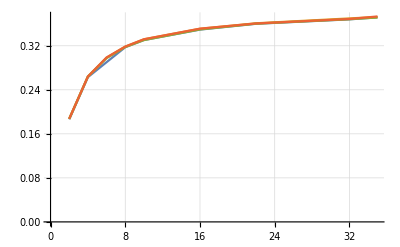

```mathematica
ListPlot[dss,Joined->True]
```

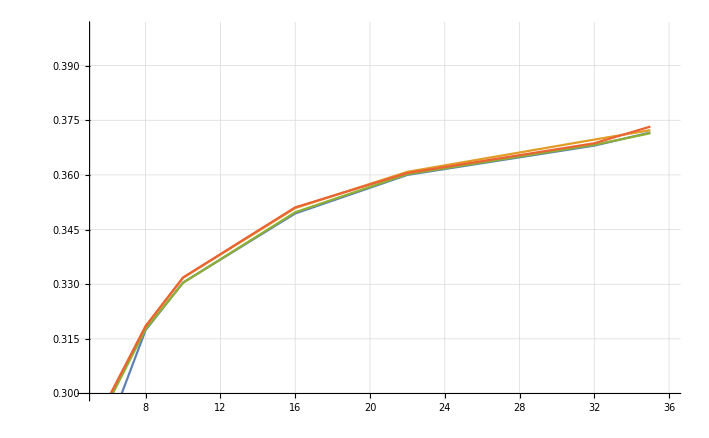

```mathematica
ListPlot[
dss,
Joined->True,PlotRange->{{5,36},{0.30,0.4}}
]
```

### mean = -1.5, sigma = 1. Plot result vs error

```mathematica
dss=ResultVsError[data, -1.5, 1, {5,52,7,71}];
```

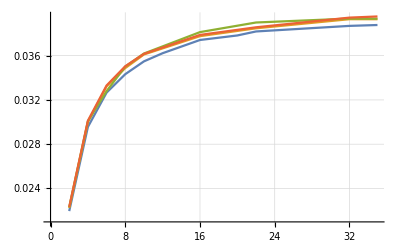

```mathematica
ListPlot[dss,Joined->True]
```

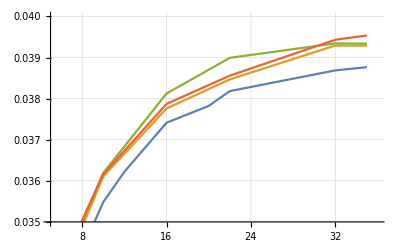

```mathematica
ListPlot[
dss,
Joined->True,PlotRange->{{5,36},{0.035,0.040}}
]
```

### Region plot

#### m = 7

```mathematica
Off[General::munfl]
```

```mathematica
d7[Select[#["mean"]==-1&&#["error"]==16 &],All]
```

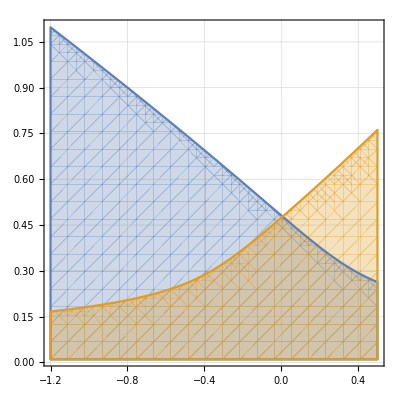

```mathematica
meanB=-1.0;sigmaB=1.0;  
ship=0.97559; s=0.8029; ksi=-0.022;
g7=RegionPlot[
{
GIndex[mean,s * sigma,ksi] <=  GIndex[meanB,s * sigmaB,ksi],
GIndex[mean,s * sigma,ksi] *ship <= mean
},
{mean, -1.2,0.5},
{sigma, 0.01,1.1}
]
```

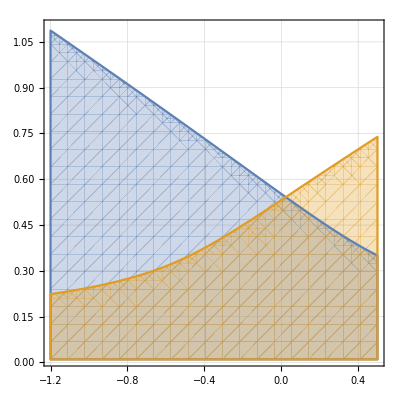

```mathematica
meanB=-1.0;sigmaB=1.0;  
ship=1.0; s=1.0; ksi=-0.06;
g7a=RegionPlot[
{
GIndex[mean,s * sigma,ksi] <=  GIndex[meanB,s * sigmaB,ksi],
GIndex[mean,s * sigma,ksi] *ship <= mean
},
{mean, -1.2,0.5},
{sigma, 0.01,1.1}
]
```

#### m = 5

```mathematica
d5[Select[#["mean"]==-1&&#["error"]==16 &],All]
```

mean + lStop * σ < meanBase + lStop * σBase
mean > (sigma-sigma0)*lShip

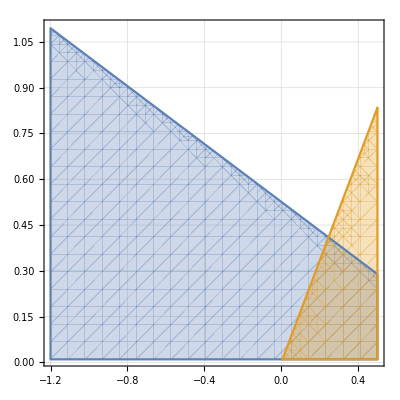

```mathematica
meanB=-1.0;sigmaB=1.0;  
 lShip=0.599; lStop=2.11; sigma0=0.0;
g5=RegionPlot[
{
PIndex[mean,sigma,lStop] <=  PIndex[meanB,sigmaB,lStop],
PIndex[-mean,sigma-sigma0,lShip]  <= PIndex[0,sigma0,ksi]
},
{mean, -1.2,0.5},
{sigma, 0.01,1.1}
]
```

#### m = 52

```mathematica
d52[Select[#["mean"]==-1&&#["error"]==15 &],All]
```

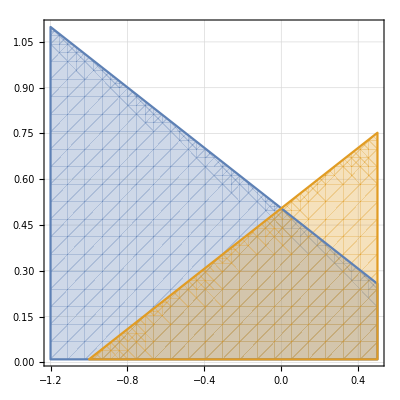

```mathematica
meanB=-1.0;sigmaB=1.0;  
 lStop=2.02;  lShip=lStop + 0.0000608;
 sigma0=PIndex[meanB, sigmaB, lStop]/lStop;
g52=RegionPlot[
{
PIndex[mean,sigma,lStop] <=  PIndex[meanB,sigmaB,lStop],
PIndex[-mean,sigma,lShip] <= PIndex[0,sigma0,lShip]
},
{mean, -1.2,0.5},
{sigma, 0.01,1.1}
]
```

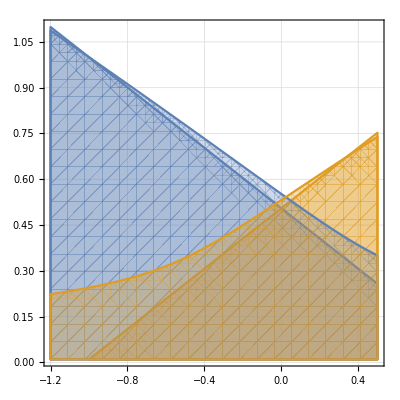

```mathematica
Show[{g52, g7a}]
```

### m=52 Regions[error=32]

```mathematica
RegionsM52[data_, error_]:=Module[
{filteredData, method, lStop, lShip, sigma0},
filteredData=data[Select[ #["error"]==error && #["m"]== 52& ]]//Sort;
((
r=#;
lStop=r["p1"];
lShip=lStop+r["p2"];
 sigma0=PIndex[r["mean"], r["sigma"], lStop]/lStop;
PIndex[mean,sigma,lStop] <=  PIndex[r["mean"],r["sigma"],lStop] ||
PIndex[-mean,sigma,lShip] <= PIndex[0,sigma0,lShip]
)&/@filteredData) // Normal
]
```

```mathematica
regs52=RegionsM52[data, 10]
```

{mean+2.8402616329643946 sigma≤0.840262||-mean+2.83600745012135 sigma≤0.839003,mean+2.765508322488381 sigma≤0.965508||-mean+2.76262865482557 sigma≤0.964503,mean+2.4881242225140063 sigma≤0.988124||-mean+2.486077066836746 sigma≤0.987311,mean+2.0115837756743313 sigma≤1.01158||-mean+2.01167 sigma≤1.01163,mean+1.2998624455213792 sigma≤0.799862||-mean+1.299619017216 sigma≤0.799713,mean+0.7634241519080012 sigma≤0.563424||-mean+0.7640612659846347 sigma≤0.563894}

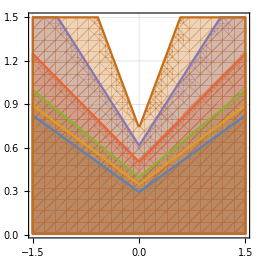

```mathematica
RegionPlot[
Evaluate[regs52//Normal],
{mean, -1.5, 1.5},
{sigma, 0.01, 1.5}
]
```

### m = 7 Regions[error = 32]

```mathematica
RegionsM7[data_, error_]:=Module[
{filteredData, method, pShip,pS,pKsi, r},
filteredData=data[Select[ #["error"]==error && #["m"]==7&& #["mean"]<0& ]]//Sort;
((
r=#;
pShip=r["p1"];
pS=r["p2"];
pKsi=r["p3"];
{
GIndex[mean,pS * sigma,pKsi] <=  GIndex[r["mean"],pS * r["sigma"],pKsi]||
GIndex[mean,pS * sigma,pKsi] *pShip <= mean,
r["mean"]
}
)&/@filteredData) // Normal//Transpose
]
```

```mathematica
{regs7, ress}=RegionsM7[data, 32];
```

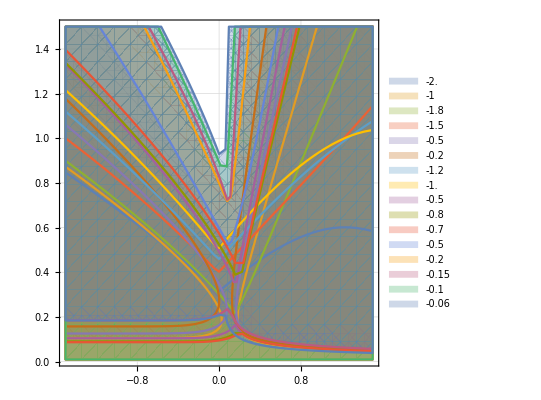

```mathematica
RegionPlot[
Evaluate[regs7//Normal],
{mean, -1.5, 1.5},
{sigma, 0.01, 1.5}, PlotLegends->ress
]
```

### m = 71 Regions[error = 32]

```mathematica
RegionsM71[data_, error_]:=Module[
{filteredData, method, pShip,pS,pKsi,meanB, sigmaB, r},
filteredData=data[Select[ #["error"]==error && #["m"]==71&& #["mean"]<0& ]]//Sort;
((
r=#;
pShip=r["p1"];
pS=r["p2"];
meanB=r["mean"];
sigmaB=r["sigma"];
pKsi=-(sigmaB*pS)^2*GIndex[meanB,pS * sigmaB,0];
{
GIndex[mean,pS * sigma,pKsi] <=  GIndex[meanB,pS *sigmaB,pKsi]||
GIndex[mean,pS * sigma,pKsi] *pShip <= mean,
r["mean"]
}
)&/@filteredData) // Normal//Transpose
]
```

```mathematica
data[Select[ #["error"]==35 && #["m"]==71&& #["mean"]<0& ]]//Sort
```

```mathematica
{regs71, ress}=RegionsM71[data, 35];
```

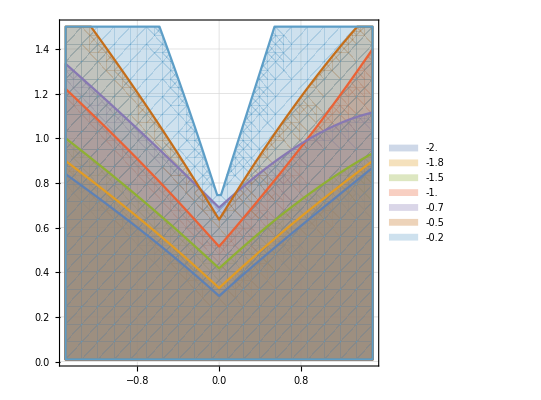

```mathematica
RegionPlot[
Evaluate[regs71//Normal],
{mean, -1.5, 1.5},
{sigma, 0.01, 1.5}, PlotLegends->ress
]
```